```mathematica
(* In this program we explore critical dimension for different values of the power 'p', mainly for p=1 (cubic nonlinearity), and p=2 (quintic nonlinearity) *)
```

## d = 4, p = 1

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* define dimension d and bounds for the r-domain *)
d=4;
p=2/(d-2);
rmin=10^(-10);
rmax=9;
tolmin = 0.001;
maxiter = 1000;
(* Equispaced grid points *)
(* b0 = 1;
bmax=100;
bvals = Range[b0,bmax]; *)
(* Grid points concentrated on smaller values of b *)
b0 = 0.36;
bmax = 10^6;
logb0=Log[b0];
logbmax =Log[bmax];
logbvals = Subdivide[logb0,logbmax,100];
bvals=Exp[logbvals];
(* Empty list to store the values λ(b) *)
lamvals = {};
(* Empty list to store the mass of u_b *)
mass = {};
(* Empty list to store elements of the form {b,λ,Subscript[f, b]} *)
solutions = {};
(* Define the ODE and the ICs *)
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+#1^3==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;
(* The j-loop goes over the b-values defined in bvals. We append the λ(b) values to lamvals *)
For[j=1,j<=Length[bvals],j++,
If[Mod[j,10]==0,Print["Iteration number ",j],];
b=bvals[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
masstmp= NIntegrate[r^(d-1)*Evaluate[f1[r]^2/.solf],{r,rmin,6}];
masstmp=masstmp[[1]];
AppendTo[mass,masstmp];
AppendTo[lamvals,λ];
AppendTo[solutions,{b,λ,f1[r]/.solf}];
]
```

Iteration number 10

Iteration number 20

Iteration number 30

Iteration number 40

Iteration number 50

Iteration number 60

Iteration number 70

Iteration number 80

Iteration number 90

Iteration number 100

```mathematica
bvals = bvals[[8;;101]];
lamvals = lamvals[[8;;101]];
```

```mathematica
bvals[[8]]
```

1.01709

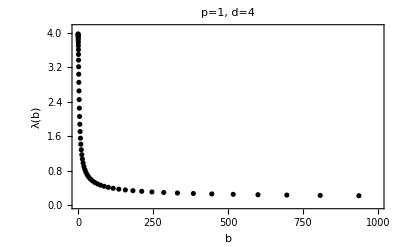

```mathematica
bversuslambdab = Transpose[{bvals,lamvals}];
plt0 =ListPlot[bversuslambdab,PlotRange->{{0,1000},{0,4.1}},LabelStyle->Directive[Black,Bold],PlotStyle->Black,PlotLabel->"p=1, d=4"];
plt1=ListLogLinearPlot[bversuslambdab,PlotRange->{{0,13000},{0,1}},PlotLegends->Placed[{"λ(b)"},Center],LabelStyle->Directive[Black,Bold],PlotStyle->Black];
bversusasympt = Transpose[{bvals,1.3/Log[bvals]}];
plt2 = ListLogLinearPlot[bversusasympt,Joined->True,PlotLegends->Placed[{"C_p/(log (b))"},Center],PlotStyle->Black,LabelStyle->Directive[Black,Bold]];
Show[plt0,Frame->True,FrameLabel->{"b","λ(b)"},RotateLabel->False]
```

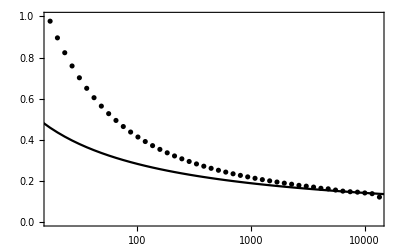

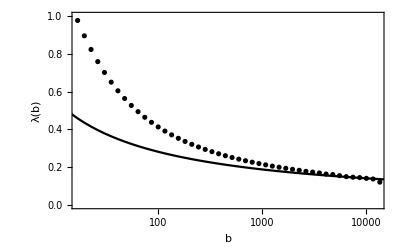

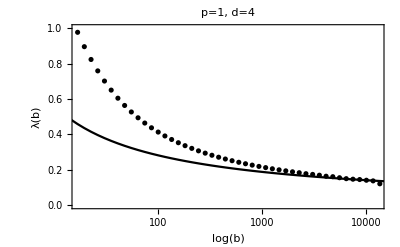

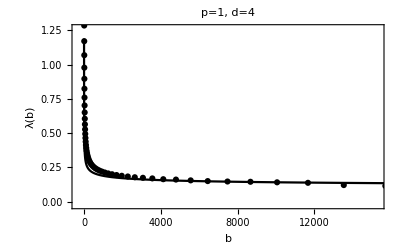

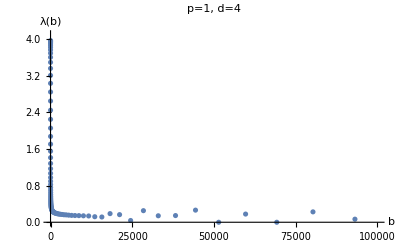

```mathematica
bversuslambdab = Transpose[{bvals,lamvals}];
ListPlot[bversuslambdab,PlotRange->{{0,10^5},{0,4.1}},AxesLabel->{"b","λ(b)"},LabelStyle->Directive[Black,Bold],PlotLabel->"p=1, d=4"]
```

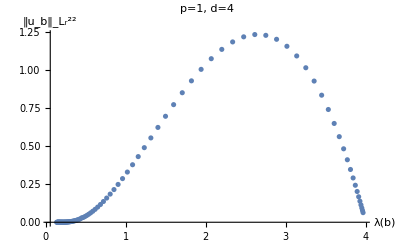

```mathematica
lambdaversusmass = Transpose[{lamvals,mass}];
ListPlot[lambdaversusmass,PlotRange->All,AxesLabel->{"λ(b)","‖u_b‖_(L_r^2)^2"},LabelStyle->Directive[Black,Bold],PlotLabel->"p=1, d=4"]
```

```mathematica
(* Plots of Subscript[f, b] for different values of λ *)
```

```mathematica
d=4;
p=2/(d-2);
rmin=10^(-10);
rmax=9;
tolmin = 0.001;
maxiter = 1000;
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+#1^3==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;
bvalues={1,2,6,10,20};
solb={};
For[j=1,j<=Length[bvalues],j++,
b=bvalues[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
AppendTo[solb,{b,λ,f1[r]/.solf}];
]
```

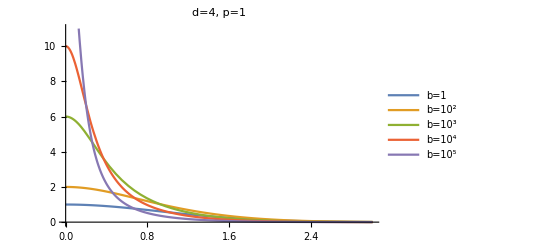
-Graphics-ru_b

```mathematica
Labeled[Plot[{solb[[1]][[3]],solb[[2]][[3]],solb[[3]][[3]],solb[[4]][[3]],solb[[5]][[3]]},{r,rmin,3},PlotRange->{0,11},PlotLabel->Style["d=4, p=1",FontSize->16,Black,FontFamily->"Times"],PlotLegends->Placed[{"b=1","b=10^2","b=10^3","b=10^4","b=10^5"},Center]],{"r","u_b"},{Bottom,Left}]
```

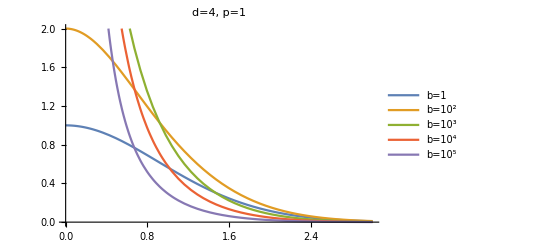
-Graphics-ru_b

```mathematica
Labeled[Plot[{solb[[1]][[3]],solb[[2]][[3]],solb[[3]][[3]],solb[[4]][[3]],solb[[5]][[3]]},{r,rmin,3},PlotRange->{0,2},PlotLabel->Style["d=4, p=1",FontSize->16,Black,FontFamily->"Times"],PlotLegends->Placed[{"b=1","b=10^2","b=10^3","b=10^4","b=10^5"},Center]],{"r","u_b"},{Bottom,Left}]
```

```mathematica
solb[[1]][[1]]
```

1

```mathematica
(* Plot algebraic solition Subscript[U, b] and Subscript[u, b] for different values of b *)
```

```mathematica
algsol[r_,b_]:=b/((1+p^2/(4(1+p))b^(2p)r^2)^(1/p));
```

```mathematica
solb[[4]][[1]]
```

10

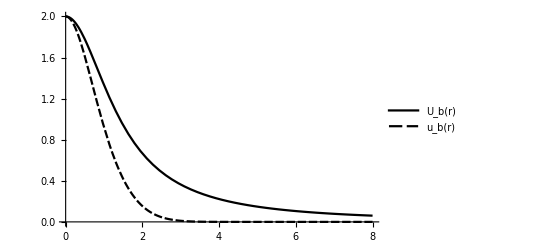
-Graphics-ru

```mathematica
Labeled[Plot[{algsol[r,solb[[2]][[1]]],solb[[2]][[3]]},{r,0,8}, PlotTheme->"Monochrome",PlotRange->All,PlotLegends->Placed[{"U_b(r)","u_b(r)"},Center],TicksStyle->Directive[Black, 14]],{"r","u"},{Bottom,Left}]
```

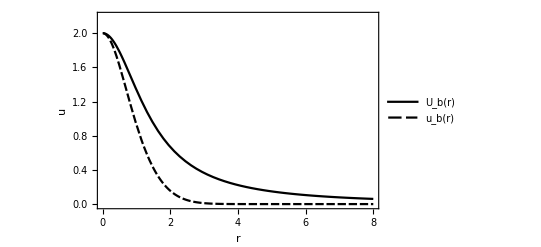

```mathematica
Plot[{algsol[r,solb[[2]][[1]]],solb[[2]][[3]]},{r,0,8}, PlotTheme->"Monochrome",PlotRange->{{0,8},{-0.01,2.2}},PlotLegends->Placed[{"U_b(r)","u_b(r)"},Center],TicksStyle->Directive[Black, 14],Frame->{{True,False},{True,False}},FrameLabel->{"r","u"},RotateLabel->False,LabelStyle->Directive[Black, Bold]]
```

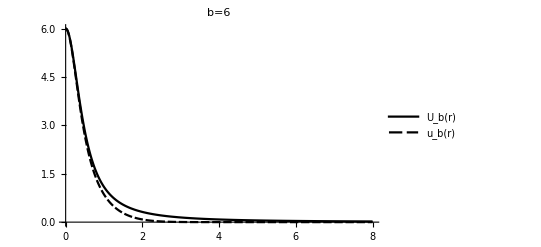
-Graphics-ru

```mathematica
Labeled[Plot[{algsol[r,solb[[3]][[1]]],solb[[3]][[3]]},{r,0,8}, PlotTheme->"Monochrome",PlotRange->All,PlotLegends->Placed[{"U_b(r)","u_b(r)"},Center],PlotLabel->Style["b=6",FontSize->16,Black,FontFamily->"Times"],TicksStyle->Directive[Black, 14]],{"r","u"},{Bottom,Left}]
```

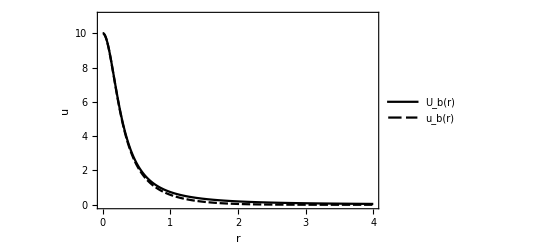

```mathematica
Plot[{algsol[r,solb[[4]][[1]]],solb[[4]][[3]]},{r,0,4}, PlotTheme->"Monochrome",PlotRange->{{0,4},{-0.01,11}},PlotLegends->Placed[{"U_b(r)","u_b(r)"},Center],Frame->{{True,False},{True,False}},FrameLabel->{"r","u"},RotateLabel->False,LabelStyle->Directive[Black, Bold]]
```

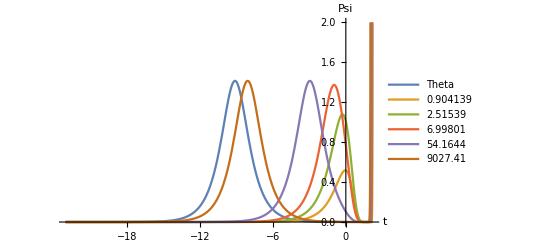

```mathematica
Plot[{Sqrt[2]*Sech[t+Log[solutions[[100]][[1]]]],Exp[t]*solutions[[10]][[3]]/.r->Exp[t],Exp[t]*solutions[[20]][[3]]/.r->Exp[t],Exp[t]*solutions[[30]][[3]]/.r->Exp[t],Exp[t]*solutions[[50]][[3]]/.r->Exp[t],Exp[t]*solutions[[100]][[3]]/.r->Exp[t]},{t,Log[rmin],Log[rmax]},PlotRange->{0,2},AxesLabel->{"t","Psi"},PlotLegends->Placed[{"Theta",solutions[[10]][[1]],solutions[[20]][[1]],solutions[[30]][[1]],solutions[[50]][[1]],solutions[[100]][[1]]},Center]]
```

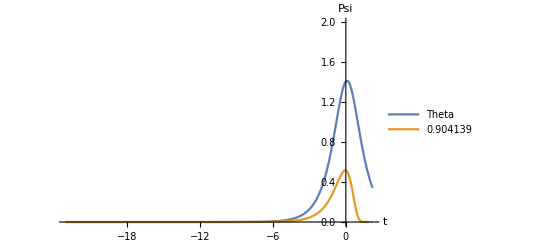

```mathematica
Plot[{Sqrt[2]*Sech[t+Log[solutions[[10]][[1]]]],Exp[t]*solutions[[10]][[3]]/.r->Exp[t]},{t,Log[rmin],Log[rmax]},PlotRange->{0,2},AxesLabel->{"t","Psi"},PlotLegends->Placed[{"Theta",solutions[[10]][[1]]},Center]]
```

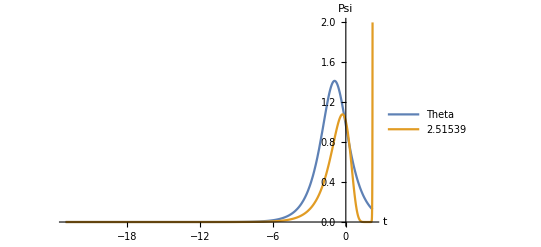

```mathematica
Plot[{Sqrt[2]*Sech[t+Log[solutions[[20]][[1]]]],Exp[t]*solutions[[20]][[3]]/.r->Exp[t]},{t,Log[rmin],Log[rmax]},PlotRange->{0,2},AxesLabel->{"t","Psi"},PlotLegends->Placed[{"Theta",solutions[[20]][[1]]},Center]]
```

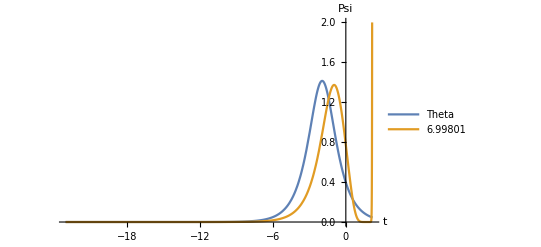

```mathematica
Plot[{Sqrt[2]*Sech[t+Log[solutions[[30]][[1]]]],Exp[t]*solutions[[30]][[3]]/.r->Exp[t]},{t,Log[rmin],Log[rmax]},PlotRange->{0,2},AxesLabel->{"t","Psi"},PlotLegends->Placed[{"Theta",solutions[[30]][[1]]},Center]]
```

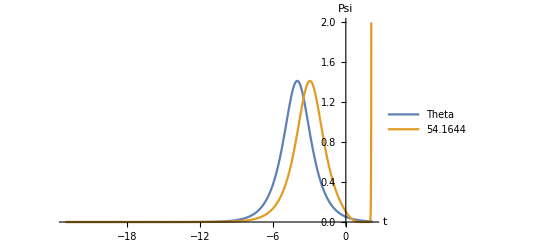

```mathematica
Plot[{Sqrt[2]*Sech[t+Log[solutions[[50]][[1]]]],Exp[t]*solutions[[50]][[3]]/.r->Exp[t]},{t,Log[rmin],Log[rmax]},PlotRange->{0,2},AxesLabel->{"t","Psi"},PlotLegends->Placed[{"Theta",solutions[[50]][[1]]},Center]]
```

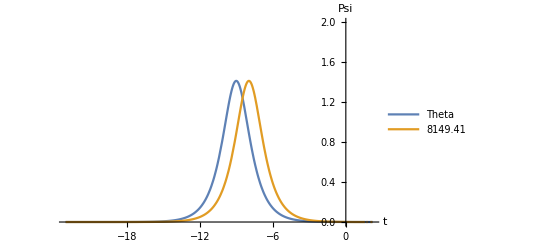

```mathematica
Plot[{Sqrt[2]*Sech[t+Log[solutions[[99]][[1]]]],Exp[t]*solutions[[99]][[3]]/.r->Exp[t]},{t,Log[rmin],Log[rmax]},PlotRange->{0,2},AxesLabel->{"t","Psi"},PlotLegends->Placed[{"Theta",solutions[[99]][[1]]},Center]]
```

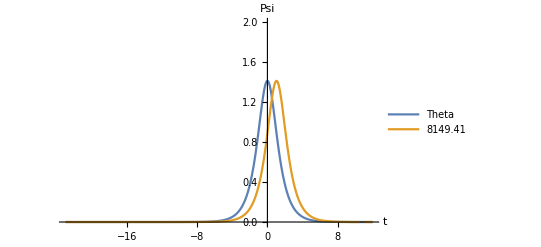

```mathematica
Plot[{Sqrt[2]*Sech[t],Exp[t-Log[solutions[[99]][[1]]]]*solutions[[99]][[3]]/.r->Exp[t-Log[solutions[[99]][[1]]]]},{t,Log[rmin],12},PlotRange->{0,2},AxesLabel->{"t","Psi"},PlotLegends->Placed[{"Theta",solutions[[99]][[1]]},Center]]
```

```mathematica
Plot[{Sqrt[2]*Sech[t+Log[1/(2*Sqrt[2])]],Exp[t-Log[solutions[[10]][[1]]]]*solutions[[10]][[3]]/.r->Exp[t-Log[solutions[[10]][[1]]]],Exp[t-Log[solutions[[20]][[1]]]]*solutions[[20]][[3]]/.r->Exp[t-Log[solutions[[20]][[1]]]],Exp[t-Log[solutions[[30]][[1]]]]*solutions[[30]][[3]]/.r->Exp[t-Log[solutions[[30]][[1]]]],Exp[t-Log[solutions[[50]][[1]]]]*solutions[[50]][[3]]/.r->Exp[t-Log[solutions[[50]][[1]]]]},{t,-10,12},PlotRange->{0,2},AxesLabel->{"t","Psi"},PlotLegends->Placed[{"Theta",solutions[[10]][[1]],solutions[[20]][[1]],solutions[[30]][[1]],solutions[[50]][[1]]},Center]]
```

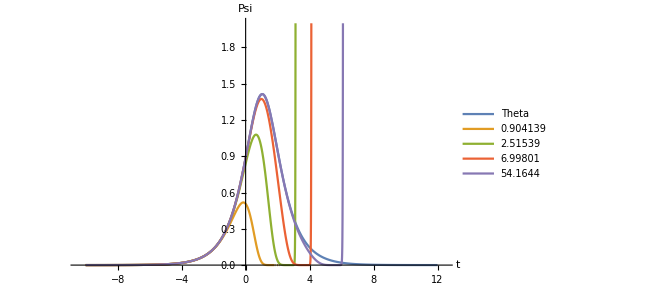

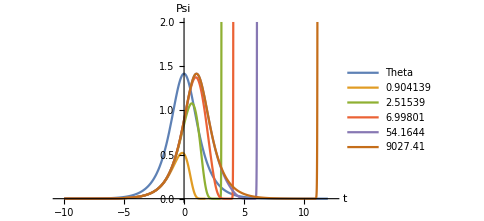

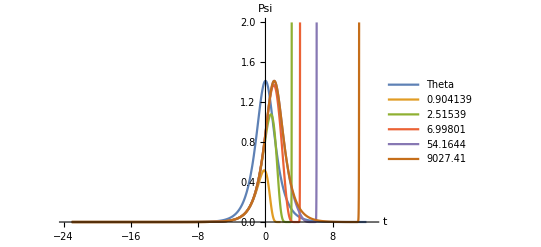

## d = 3, p = 2

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* define dimension d and bounds for the r-domain *)
d=3;
p=2/(d-2);
rmin=10^(-10);
rmax=9;
tolmin = 0.001;
maxiter = 1000;
(* Equispaced grid points *)
(* b0 = 1;
bmax=100;
bvals = Range[b0,bmax]; *)
(* Grid points concentrated on smaller values of b *)
b0 = 0.36;
bmax = 10000;
logb0=Log[b0];
logbmax =Log[bmax];
logbvals = Subdivide[logb0,logbmax,100];
bvals=Exp[logbvals];
(* Empty list to store the values λ(b) *)
lamvals = {};
(* Empty list to store the mass of u_b *)
mass = {};
(* Empty list to store elements of the form {b,λ,Subscript[f, b]} *)
solutions = {};
(* Define the ODE and the ICs *)
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+#1^5==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;
(* The j-loop goes over the b-values defined in bvals. We append the λ(b) values to lamvals *)
For[j=1,j<=Length[bvals],j++,
If[Mod[j,10]==0,Print["Iteration number ",j],];
b=bvals[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
masstmp= NIntegrate[r^(d-1)*Evaluate[f1[r]^2/.solf],{r,rmin,6}];
masstmp=masstmp[[1]];
AppendTo[mass,masstmp];
AppendTo[lamvals,λ];
AppendTo[solutions,{b,λ,f1[r]/.solf}];
]
```

Iteration number 10

Iteration number 20

Iteration number 30

Iteration number 40

Iteration number 50

Iteration number 60

Iteration number 70

Iteration number 80

Iteration number 90

Iteration number 100

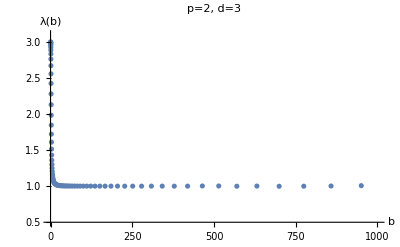

```mathematica
bversuslambdab = Transpose[{bvals,lamvals}];
ListPlot[bversuslambdab,PlotRange->{{0,1000},{0.5,3.1}},AxesLabel->{"b","λ(b)"},LabelStyle->Directive[Black,Bold],PlotLabel->"p=2, d=3"]
```

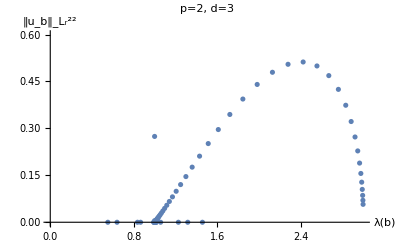

```mathematica
lambdaversusmass = Transpose[{lamvals,mass}];
ListPlot[lambdaversusmass,PlotRange->{0,0.6},AxesLabel->{"λ(b)","‖u_b‖_(L_r^2)^2"},LabelStyle->Directive[Black,Bold],PlotLabel->"p=2, d=3"]
```

```mathematica
(* Plot Subscript[f, b] for different values of b *)
```

```mathematica
d=3;
p=2/(d-2);
rmin=10^(-10);
rmax=9;
tolmin = 0.001;
maxiter = 1000;
bvalues={1,2,6,10,20};
solb={};
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+#1^5==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;
For[j=1,j<=Length[bvalues],j++,
b=bvalues[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
AppendTo[solb,{b,λ,f1[r]/.solf}];
]
```

```mathematica
(* Plot algebraic solition Subscript[U, b] and Subscript[u, b] for different values of b *)
```

```mathematica
algsol[r_,b_]:=b/((1+p^2/(4(1+p))b^(2p)r^2)^(1/p));
```

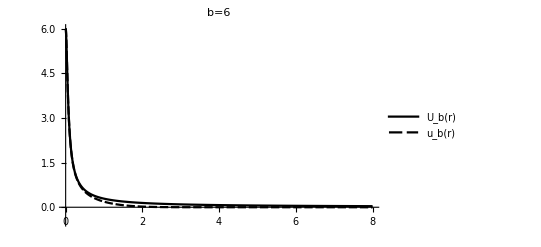

```mathematica
Plot[{algsol[r,solb[[3]][[1]]],solb[[3]][[3]]},{r,0,8}, PlotTheme->"Monochrome",PlotRange->{{0,8},{-0.5,solb[[3]][[1]]}},PlotLegends->Placed[{"U_b(r)","u_b(r)"},Center],PlotLabel->Style["b=6",FontSize->16,Black,FontFamily->"Times"],TicksStyle->Directive[Black, 14]]
```

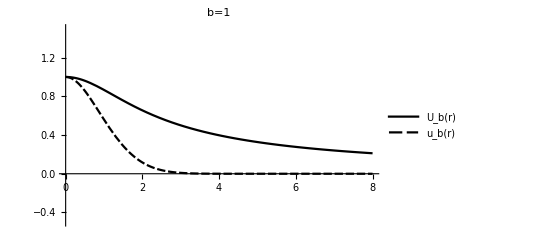

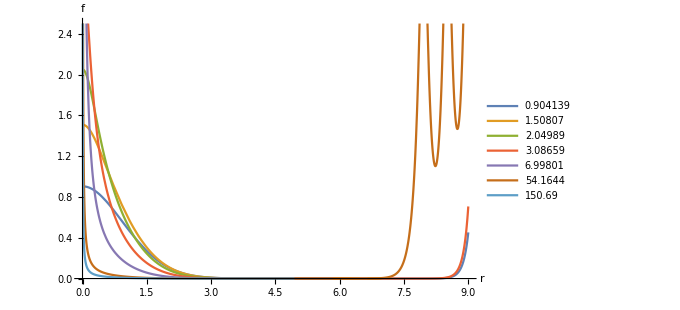

```mathematica
Plot[{solutions[[10]][[3]],solutions[[15]][[3]],solutions[[18]][[3]],solutions[[22]][[3]],solutions[[30]][[3]],solutions[[50]][[3]],solutions[[60]][[3]]},{r,rmin,rmax},PlotRange->{0,2.5},AxesLabel->{"r","f"},PlotLegends->Placed[{solutions[[10]][[1]],solutions[[15]][[1]],solutions[[18]][[1]],solutions[[22]][[1]],solutions[[30]][[1]],solutions[[50]][[1]],solutions[[60]][[1]]},Center]]
```

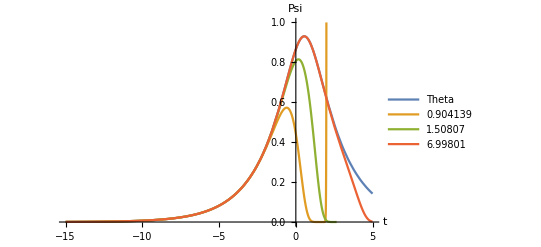

```mathematica
Plot[{(Exp[t]/(1+p^2/(4(1+p))Exp[2t]))^(1/p),Exp[(t-p Log[solutions[[10]][[1]]])/p]*solutions[[10]][[3]]/.r->Exp[t-p Log[solutions[[10]][[1]]]],Exp[(t-p Log[solutions[[15]][[1]]])/p]*solutions[[15]][[3]]/.r->Exp[t-p Log[solutions[[15]][[1]]]],Exp[(t-p Log[solutions[[30]][[1]]])/p]*solutions[[30]][[3]]/.r->Exp[t-p Log[solutions[[30]][[1]]]]},{t,-15,5},PlotRange->{0,1},AxesLabel->{"t","Psi"},PlotLegends->Placed[{"Theta",solutions[[10]][[1]],solutions[[15]][[1]],solutions[[30]][[1]],solutions[[50]][[1]],solutions[[100]][[1]]},Center]]
```

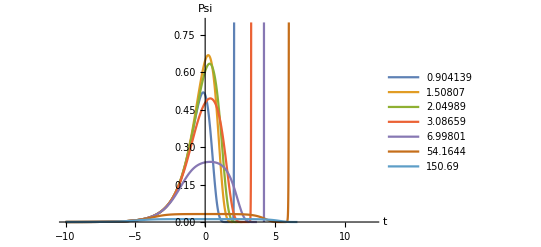

```mathematica
Plot[{Exp[t-Log[solutions[[10]][[1]]]]*solutions[[10]][[3]]/.r->Exp[t-Log[solutions[[10]][[1]]]],Exp[t-Log[solutions[[15]][[1]]]]*solutions[[15]][[3]]/.r->Exp[t-Log[solutions[[15]][[1]]]],Exp[t-Log[solutions[[18]][[1]]]]*solutions[[18]][[3]]/.r->Exp[t-Log[solutions[[18]][[1]]]],Exp[t-Log[solutions[[22]][[1]]]]*solutions[[22]][[3]]/.r->Exp[t-Log[solutions[[22]][[1]]]],Exp[t-Log[solutions[[30]][[1]]]]*solutions[[30]][[3]]/.r->Exp[t-Log[solutions[[30]][[1]]]],Exp[t-Log[solutions[[50]][[1]]]]*solutions[[50]][[3]]/.r->Exp[t-Log[solutions[[50]][[1]]]],Exp[t-Log[solutions[[60]][[1]]]]*solutions[[60]][[3]]/.r->Exp[t-Log[solutions[[60]][[1]]]]},{t,-10,12},PlotRange->{0,0.8},AxesLabel->{"t","Psi"},PlotLegends->Placed[{solutions[[10]][[1]],solutions[[15]][[1]],solutions[[18]][[1]],solutions[[22]][[1]],solutions[[30]][[1]],solutions[[50]][[1]],solutions[[60]][[1]]},Center]]
```

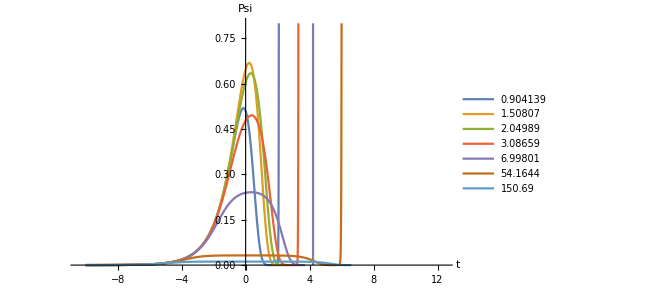

## d = 6, p = 1/2

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* define dimension d and bounds for the r-domain *)
d=6;
rmin=10^(-5);
rmax=9;
tolmin = 0.001;
maxiter = 1000;
(* Equispaced grid points *)
(* b0 = 1;
bmax=100;
bvals = Range[b0,bmax]; *)
(* Grid points concentrated on smaller values of b *)
b0 = 0.36;
bmax = 10000;
logb0=Log[b0];
logbmax =Log[bmax];
logbvals = Subdivide[logb0,logbmax,100];
bvals=Exp[logbvals];
(* Empty list to store the values λ(b) *)
lamvals = {};
(* Empty list to store the mass of u_b *)
mass = {};
(* Empty list to store elements of the form {b,λ,Subscript[f, b]} *)
solutions = {};
(* Define the ODE and the ICs *)
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+#1^2==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;
(* The j-loop goes over the b-values defined in bvals. We append the λ(b) values to lamvals *)
For[j=1,j<=Length[bvals],j++,
If[Mod[j,10]==0,Print["Iteration number ",j],];
b=bvals[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
masstmp= NIntegrate[r^(d-1)*Evaluate[f1[r]^2/.solf],{r,rmin,6}];
masstmp=masstmp[[1]];
AppendTo[mass,masstmp];
AppendTo[lamvals,λ];
AppendTo[solutions,{b,λ,f1[r]/.solf}];
]
```

NDSolve::ndsz: At r == 6.76716, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {9} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At r == 6.90891, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At r == 7.06897, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

Iteration number 10

Iteration number 20

Iteration number 30

Iteration number 40

Iteration number 50

Iteration number 60

Iteration number 70

Iteration number 80

Iteration number 90

Iteration number 100

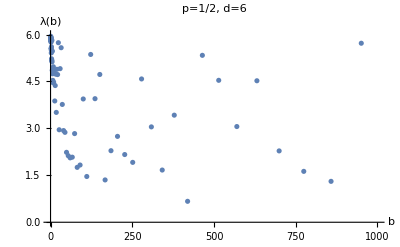

```mathematica
bversuslambdab = Transpose[{bvals,lamvals}];
ListPlot[bversuslambdab,PlotRange->{{0,1000},{0,d}},AxesLabel->{"b","λ(b)"},LabelStyle->Directive[Black,Bold],PlotLabel->"p=1/2, d=6"]
```

```mathematica
lambdaversusmass = Transpose[{lamvals,mass}];
ListPlot[lambdaversusmass,PlotRange->Automatic,AxesLabel->{"λ(b)","‖u_b‖_(L_r^2)^2"},LabelStyle->Directive[Black,Bold],PlotLabel->"p=1/2, d=6"]
```

-Graphics-

```mathematica
Plot[{solutions[[10]][[3]],solutions[[15]][[3]],solutions[[18]][[3]],solutions[[22]][[3]],solutions[[30]][[3]],solutions[[50]][[3]],solutions[[60]][[3]]},{r,rmin,rmax},PlotRange->{-50,56},AxesLabel->{"r","f"},PlotLegends->Placed[{solutions[[10]][[1]],solutions[[15]][[1]],solutions[[18]][[1]],solutions[[22]][[1]],solutions[[30]][[1]],solutions[[50]][[1]],solutions[[60]][[1]]},Center]]
```

```mathematica
Plot[{Exp[t]*solutions[[10]][[3]]/.r->Exp[t],Exp[t]*solutions[[15]][[3]]/.r->Exp[t],Exp[t]*solutions[[18]][[3]]/.r->Exp[t],Exp[t]*solutions[[22]][[3]]/.r->Exp[t],Exp[t]*solutions[[30]][[3]]/.r->Exp[t],Exp[t]*solutions[[50]][[3]]/.r->Exp[t]},{t,Log[rmin],Log[rmax]},PlotRange->{0,1},AxesLabel->{"t","Psi"},PlotLegends->Placed[{"Theta",solutions[[10]][[1]],solutions[[20]][[1]],solutions[[30]][[1]],solutions[[50]][[1]],solutions[[100]][[1]]},Center]]
```

```mathematica
Plot[{Exp[t-Log[solutions[[10]][[1]]]]*solutions[[10]][[3]]/.r->Exp[t-Log[solutions[[10]][[1]]]],Exp[t-Log[solutions[[15]][[1]]]]*solutions[[15]][[3]]/.r->Exp[t-Log[solutions[[15]][[1]]]],Exp[t-Log[solutions[[18]][[1]]]]*solutions[[18]][[3]]/.r->Exp[t-Log[solutions[[18]][[1]]]],Exp[t-Log[solutions[[22]][[1]]]]*solutions[[22]][[3]]/.r->Exp[t-Log[solutions[[22]][[1]]]],Exp[t-Log[solutions[[30]][[1]]]]*solutions[[30]][[3]]/.r->Exp[t-Log[solutions[[30]][[1]]]],Exp[t-Log[solutions[[50]][[1]]]]*solutions[[50]][[3]]/.r->Exp[t-Log[solutions[[50]][[1]]]],Exp[t-Log[solutions[[60]][[1]]]]*solutions[[60]][[3]]/.r->Exp[t-Log[solutions[[60]][[1]]]]},{t,-10,12},PlotRange->{0,0.8},AxesLabel->{"t","Psi"},PlotLegends->Placed[{solutions[[10]][[1]],solutions[[15]][[1]],solutions[[18]][[1]],solutions[[22]][[1]],solutions[[30]][[1]],solutions[[50]][[1]],solutions[[60]][[1]]},Center]]
```

## d = 5, p = 0.67

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* define dimension d and bounds for the r-domain *)
d=5;
p=2/(d-2);
rmin=10^(-10);
rmax=4;
tolmin = 0.001;
maxiter = 1000;
(* Equispaced grid points *)
(* b0 = 1;
bmax=100;
bvals = Range[b0,bmax]; *)
(* Grid points concentrated on smaller values of b *)
b0 = 0.36;
bmax = 10^6;
logb0=Log[b0];
logbmax =Log[bmax];
logbvals = Subdivide[logb0,logbmax,100];
bvals=Exp[logbvals];
(* Empty list to store the values λ(b) *)
lamvals = {};
(* Empty list to store the mass of u_b *)
mass = {};
(* Empty list to store elements of the form {b,λ,Subscript[f, b]} *)
solutions = {};
(* Define the ODE and the ICs *)
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+Abs[#1]^(2p+1)==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;
(* The j-loop goes over the b-values defined in bvals. We append the λ(b) values to lamvals *)
For[j=1,j<=Length[bvals],j++,
If[Mod[j,10]==0,Print["Iteration number ",j],];
b=bvals[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
masstmp= NIntegrate[r^(d-1)*Evaluate[f1[r]^2/.solf],{r,rmin,6}];
masstmp=masstmp[[1]];
AppendTo[mass,masstmp];
AppendTo[lamvals,λ];
AppendTo[solutions,{b,λ,f1[r]/.solf}];
]
```

Iteration number 10

Iteration number 20

Iteration number 30

Iteration number 40

Iteration number 50

Iteration number 60

Iteration number 70

Iteration number 80

Iteration number 90

Iteration number 100

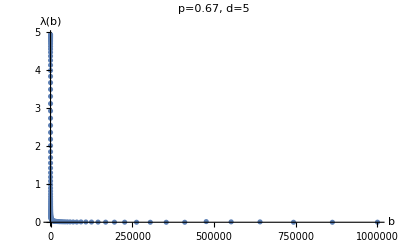

```mathematica
bversuslambdab = Transpose[{bvals,lamvals}];
ListPlot[bversuslambdab,PlotRange->All,AxesLabel->{"b","λ(b)"},LabelStyle->Directive[Black,Bold],PlotLabel->"p=0.67, d=5"]
```

```mathematica
bversuslambdab = Transpose[{Log[bvals],Log[lamvals]}];
plt1=ListPlot[bversuslambdab,PlotRange->All,LabelStyle->Directive[Black,Bold],PlotLegends->Placed[{"log(λ(b))"},Center],PlotStyle->Black];
bversusasympt = Transpose[{Log[bvals],-2(1-p)Log[bvals]+2.7}];
plt2 = ListPlot[bversusasympt,Joined->True,PlotLegends->Placed[{"-1.33log(b)+log(C_p)"},Center],PlotStyle->Black,LabelStyle->Directive[Black,Bold]];
Show[plt1,plt2,PlotRange->{{-1,10},{-4,4}},Frame->True,FrameLabel->{"log(b)"},RotateLabel->False]
```

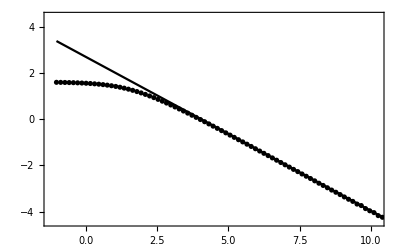

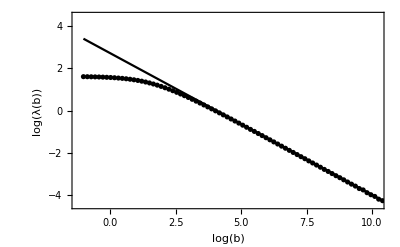

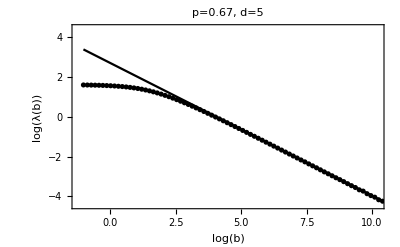

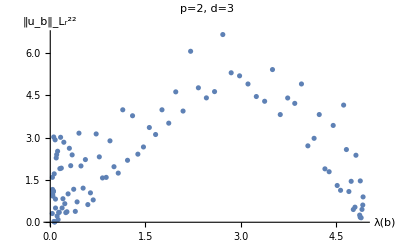

```mathematica
lambdaversusmass = Transpose[{lamvals,mass}];
ListPlot[lambdaversusmass,PlotRange->All,AxesLabel->{"λ(b)","‖u_b‖_(L_r^2)^2"},LabelStyle->Directive[Black,Bold],PlotLabel->"p=2, d=3"]
```

```mathematica
(* Plot Subscript[f, b] for different values of b *)
```

```mathematica
bvalues={1,2,6,10,20};
solb={};
For[j=1,j<=Length[bvalues],j++,
b=bvalues[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
AppendTo[solb,{b,λ,f1[r]/.solf}];
]
```

```mathematica
(* Plot algebraic solition Subscript[U, b] and Subscript[u, b] for different values of b *)
```

```mathematica
algsol[r_,b_]:=b/((1+p^2/(4(1+p))b^(2p)r^2)^(1/p));
```

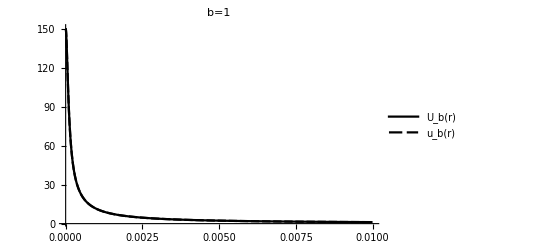
-Graphics-ru

```mathematica
Labeled[Plot[{algsol[r,solutions[[60]][[1]]],solutions[[60]][[3]]},{r,0,0.01}, PlotTheme->"Monochrome",PlotRange->All,PlotLegends->Placed[{"U_b(r)","u_b(r)"},Center],PlotLabel->Style["b=1",FontSize->16,Black,FontFamily->"Times"],TicksStyle->Directive[Black, 14]],{"r","u"},{Bottom,Left}]
```

## d = 7, p = 0.4

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* define dimension d and bounds for the r-domain *)
d=7;
p=2/(d-2);
rmin=10^(-10);
rmax=2.5;
tolmin = 0.001;
maxiter = 1000;
(* Equispaced grid points *)
(* b0 = 1;
bmax=100;
bvals = Range[b0,bmax]; *)
(* Grid points concentrated on smaller values of b *)
b0 = 0.36;
bmax = 10^6;
logb0=Log[b0];
logbmax =Log[bmax];
logbvals = Subdivide[logb0,logbmax,100];
bvals=Exp[logbvals];
(* Empty list to store the values λ(b) *)
lamvals = {};
(* Empty list to store the mass of u_b *)
mass = {};
(* Empty list to store elements of the form {b,λ,Subscript[f, b]} *)
solutions = {};
(* Define the ODE and the ICs *)
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+Abs[#1]^(2p+1)==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;
(* The j-loop goes over the b-values defined in bvals. We append the λ(b) values to lamvals *)
For[j=1,j<=Length[bvals],j++,
If[Mod[j,10]==0,Print["Iteration number ",j],];
b=bvals[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
masstmp= NIntegrate[r^(d-1)*Evaluate[f1[r]^2/.solf],{r,rmin,6}];
masstmp=masstmp[[1]];
AppendTo[mass,masstmp];
AppendTo[lamvals,λ];
AppendTo[solutions,{b,λ,f1[r]/.solf}];
]
```

Iteration number 10

Iteration number 20

Iteration number 30

Iteration number 40

Iteration number 50

Iteration number 60

Iteration number 70

Iteration number 80

Iteration number 90

Iteration number 100

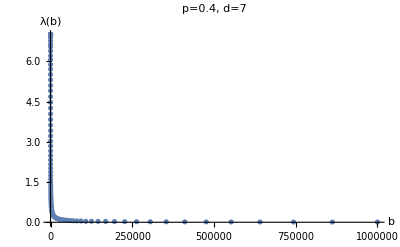

```mathematica
bversuslambdab = Transpose[{bvals,lamvals}];
ListPlot[bversuslambdab,PlotRange->All,AxesLabel->{"b","λ(b)"},LabelStyle->Directive[Black,Bold],PlotLabel->"p=0.4, d=7"]
```

```mathematica
bversuslambdab = Transpose[{Log[bvals],Log[lamvals]}];
plt1=ListPlot[bversuslambdab,PlotRange->All,LabelStyle->Directive[Black,Bold],PlotLegends->Placed[{"log(λ(b))"},Center],PlotStyle->Black];
bversusasympt = Transpose[{Log[bvals],-2p Log[bvals]+6.1}];
plt2 = ListPlot[bversusasympt,Joined->True,PlotLegends->Placed[{"-0.8log(b)+log(C_p)"},Center],PlotStyle->Black,LabelStyle->Directive[Black,Bold]];
Show[plt1,plt2,PlotRange->{{-1,10},{-2,5}},Frame->True,FrameLabel->{"log(b)"},RotateLabel->False]
```

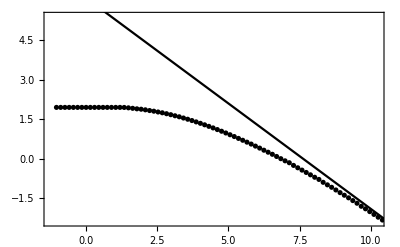

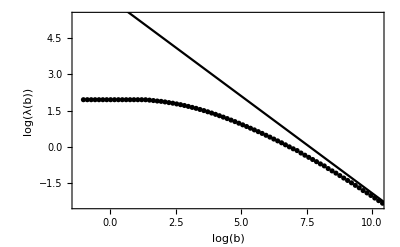

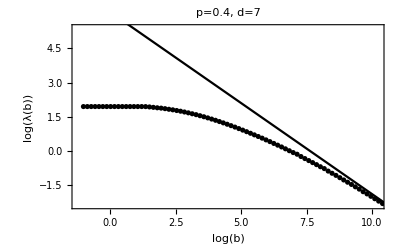

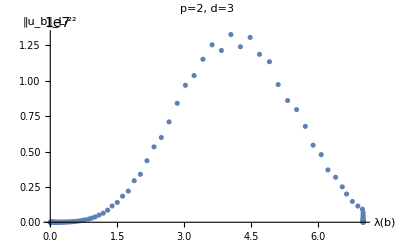

```mathematica
lambdaversusmass = Transpose[{lamvals,mass}];
ListPlot[lambdaversusmass,PlotRange->All,AxesLabel->{"λ(b)","‖u_b‖_(L_r^2)^2"},LabelStyle->Directive[Black,Bold],PlotLabel->"p=2, d=3"]
```

## Find f_b for a given b, d, and p=2/(d-2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* define dimension d and bounds for the r-domain *)
d=5;
p=2/(d-2);
rmin=10^(-5);
rmax=4;
tolmin = 0.001;
maxiter = 1000;
b = 10;
(* Empty list to store the values λ(b) *)
lamvals = {};
(* Empty list to store the mass of u_b *)
mass = {};
(* Empty list to store elements of the form {b,λ,Subscript[f, b]} *)
solutions = {};
(* Define the ODE and the ICs *)
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+Abs[#1]^(2p+1)==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;

(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];

AppendTo[lamvals,λ];
AppendTo[solutions,{b,λ,f1[r]/.solf}];
```

```mathematica
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,8},Method->"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic},AccuracyGoal->6,PrecisionGoal->6];
```

NDSolve::ndsz: At r == 4.50413, step size is effectively zero; singularity or stiff system suspected.

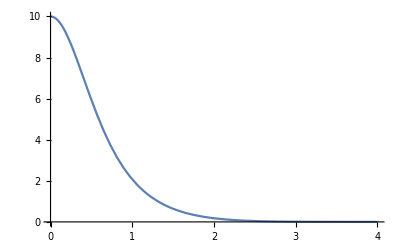

```mathematica
Plot[solutions[[1]][[3]],{r,rmin,rmax}]
```

## tests

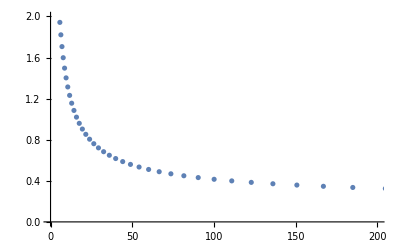

```mathematica
ListPlot[bversuslambdab,PlotRange->{{0,200},{0,2}}]
```

```mathematica
sol1=NDSolve[{NL2[f1[r],f2[r],lamvals[[35]]],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
sol2=NDSolve[{NL2[f1[r],f2[r],lamvals[[41]]],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
sol3=NDSolve[{NL2[f1[r],f2[r],lamvals[[45]]],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
sol4=NDSolve[{NL2[f1[r],f2[r],lamvals[[49]]],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
sol5=NDSolve[{NL2[f1[r],f2[r],lamvals[[51]]],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
```

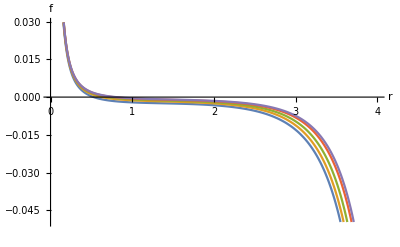

```mathematica
Plot[{Evaluate[f1[r]/.sol1],Evaluate[f1[r]/.sol2],Evaluate[f1[r]/.sol3],Evaluate[f1[r]/.sol4],Evaluate[f1[r]/.sol5]},{r,0,4},AxesLabel->{"r","f"}]
```

```mathematica
p
```

2

```mathematica
(* define dimension d and bounds for the r-domain *)
d=5;
p=2/(d-2);
rmin=10^(-10);
rmax=9;
tolmin = 0.001;
maxiter = 1000;
b = 10;
(* Empty list to store the values λ(b) *)
lamvals = {};
(* Empty list to store the mass of u_b *)
mass = {};
(* Empty list to store elements of the form {b,λ,Subscript[f, b]} *)
solutions = {};
(* Define the ODE and the ICs *)
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+Abs[#1]^(2p+1)==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;

(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
```

```mathematica
Plot[{6+2/x+2*Sqrt[4+2/x],10,6+2/x+2*Sqrt[4+2/x]},{x,0,6},AxesLabel->{Style["p",Bold,Black,12],Style["d",Bold,Black,12]},PlotRange->{{0,6},{0,30}},PlotStyle->{{Black},{Black,Dashed}},Filling->{1->{Axis,Directive[Opacity[0.5],Orange]},3->{Top,Directive[Opacity[0.3],Blue]}}]
```